```mathematica
SetDirectory[NotebookDirectory[]] ;
errors = Import["errors.dat"];
data = Import["solution.dat"];
dataquad = Import["solution_quad.dat"];
datasimple= Import["solution_simple.dat"];
```

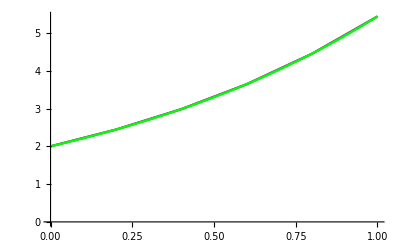

```mathematica
Show[ListLinePlot[dataquad,PlotStyle->Red],ListLinePlot[datasimple], Plot[2Exp[t], {t, 0, 1}, PlotStyle->Green]]
```

```mathematica
(*eq={y[x]-λ∫_a^b k[x,s]*y[s]ⅆs==f[x]};
params = {a->0,b->1,k[x,s]->0.5(1-x *Cos[x *s]),f[x]->0.5(1+Sin[x])};
params1 = {a->0,b->1,k[x,s]->1,f[x]->0.5(1+Sin[x])};*)
```

```mathematica
(*eq=eq/.params;
DSolveValue[eq[[1]],y[x],x]*)
```

```mathematica
errors2=Table[{i, MaxNorm[]},{i,1,Length@errors}]
```

{{1,0},{2,4.48368×10^-6},{3,6.04717×10^-7},{4,2.39922×10^-6},{5,1.85698×10^-6},{6,3.65692×10^-6}}

```mathematica
logerrors=({#[[1]],Log[#[[2]]]})&/@errors2;
```

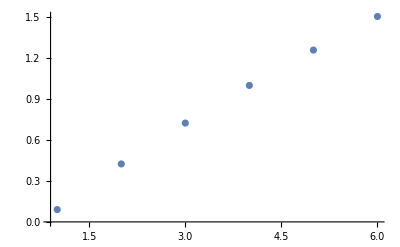

```mathematica
ListPlot[logerrors, PlotRange->Full]
```

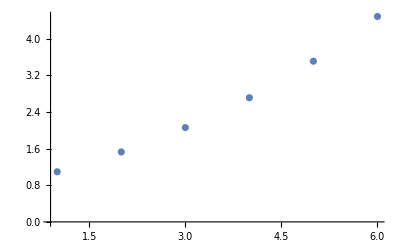

```mathematica
ListPlot[errors2, PlotRange->All]
```

```mathematica
Grid[{{"Iters","|err|"}}~Join~errors2, Frame->All, Spacings -> {1, 1}]
```

Iters | |err|
1 | 1.09429
2 | 1.52704
3 | 2.05822
4 | 2.70948
5 | 3.50728
6 | 4.48394

```mathematica
datah=Import["solution_h.dat"];
data2h=Import["solution_2h.dat"];
data4h=Import["solution_4h.dat"];
G[x_]:=2Exp[x];
```

```mathematica
MaxNorm[data_,G_]:=Max[Table[Abs[G[data[[i,1]]]-data[[i,2]]],{i,1,Length@data}]];
```

```mathematica
norms={{"h",MaxNorm[datah,G]},{"2h",MaxNorm[data2h,G]},{"4h",MaxNorm[data4h,G]}};
```

```mathematica
Grid[norms, Frame-> All, Spacings->{1, 1}]
```

h | 4.90281×10^-6
2h | 4.58506×10^-6
4h | 4.48368×10^-6

```mathematica
ListPointPlot3D[datasingular, AxesLabel->{"x", "y", "Res"},AxesOrigin->{0,0,0}]
```